```mathematica
d=Import["C:\\Users\\Administrator\\Documents\\Wolfram Mathematica\\data.txt"];
```

### n max部分结果

```mathematica
n=11;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];r2=2^n;
```

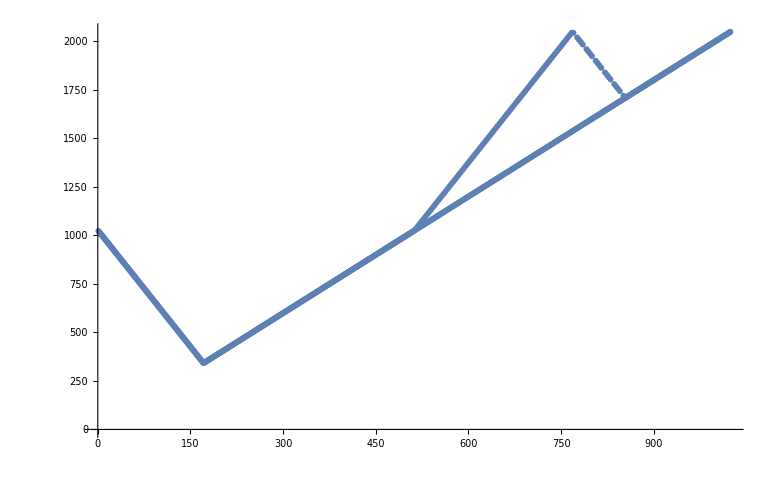

```mathematica
ans = Table[p1=Mod[q r,r2];p2=r2-p1;t=If[GCD[p1,q]==  1,If[GCD[p2,q]==  1,Max[{Min[{p1,p2}],q}],Max[{p1,q}]],If[GCD[p2,q]==  1,Max[{p2,q}],∞]];t,{q,1,r2,2}];
ListPlot[{ans}]
```

### 是否会出现gcd(p,q) ≠ 1 但gcd(2^n-p,q)=1的情况

```mathematica
n=3;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];r2=2^n;q=1;result={0,0,0,0};
While[q<r2,p=Mod[q r,r2];If[GCD[p,q]==1,
If[GCD[r2-p,q]==1,result[[1]]= result[[1]]+1,result[[2]]=result[[2]]+1],
If[GCD[r2-p,q]==1,Print[q];Break[];result[[3]]=result[[3]]+1,result[[4]]=result[[4]]+1]];q=q+2];
result
```

3

{1,0,0,0}

### 部分列举并画图展示

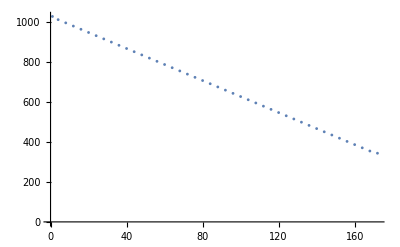

```mathematica
n=13;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];Subscript[r, 2]=2^n;min=∞;
ans = Table[Subscript[p, 1]=Mod[q r,Subscript[r, 2]];Subscript[p, 2]=Subscript[r, 2]-Subscript[p, 1];t=If[GCD[Subscript[p, 1],q]==  1,If[GCD[Subscript[p, 2],q]==  1,Max[{Min[{Subscript[p, 1],Subscript[p, 2]}],q}],Max[{Subscript[p, 1],q}]],If[GCD[Subscript[p, 2],q]==  1,Max[{Subscript[p, 2],q}],∞]];If[t<min,min=t,∞],{q,1,2^n-1,2}];
ListPlot[{ans},PlotStyle->PointSize[0.005]]
```

```mathematica
n=13;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];Subscript[r, 2]=2^n;min=∞;
Subscript[ans, 2] = Table[Subscript[p, 1]=Mod[q r,Subscript[r, 2]];Subscript[p, 2]=Subscript[r, 2]-Subscript[p, 1];t=If[GCD[Subscript[p, 1],q]==  1,If[GCD[Subscript[p, 2],q]==  1,Max[{Min[{Subscript[p, 1],Subscript[p, 2]}],q}],Max[{Subscript[p, 1],q}]],If[GCD[Subscript[p, 2],q]==  1,Max[{Subscript[p, 2],q}],∞]];If[t>1 10^13,∞,t],{q,1,2000,2}];
ListPlot[{Subscript[ans, 2]},PlotStyle->PointSize[0.005]]
```

### 最小值点位置探索

```mathematica
n=100;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];Subscript[r, 2]=2^n;min=∞;
```

```mathematica
ans = Table[Subscript[p, 1]=Mod[q r,Subscript[r, 2]];Subscript[p, 2]=Subscript[r, 2]-Subscript[p, 1];t=If[GCD[Subscript[p, 1],q]==  1,If[GCD[Subscript[p, 2],q]==  1,Max[{Min[{Subscript[p, 1],Subscript[p, 2]}],q}],Max[{Subscript[p, 1],q}]],If[GCD[Subscript[p, 2],q]==  1,Max[{Subscript[p, 2],q}],∞]];t=If[t<min,min=t,∞];If[t>1 10^29,∞,t],{q,1,100000,2}];

ListPlot[{ans},PlotStyle->PointSize[0.005]]
```

-Graphics-

### 寻找

```mathematica
StringLength[d]
```

1966000

```mathematica
n=1966000;r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];r2=2^n;
```

```mathematica
q=2^(n-10)+1;nn=0;
While[True,p1=Mod[q r,r2];p2=r2-p1;t=If[GCD[p1,q]==  1,If[GCD[p2,q]==  1,Max[{Min[{p1,p2}],q}],Max[{p1,q}]],If[GCD[p2,q]==  1,Max[{p2,q}],∞]];If[t==q,Print[nn];Break[],0];q = q +2;nn = nn + 1];
```

$Aborted

### 验证最小值是否都为q的某个值

```mathematica
r=0;Transpose[Table[r=r+ If[StringTake[d,{n}]=="1",2^(n-1),0];Subscript[r, 2]=2^n;min=∞;q=1;
While[True,Subscript[p, 1]=Mod[q r,Subscript[r, 2]];Subscript[p, 2]=Subscript[r, 2]-Subscript[p, 1];t=If[GCD[Subscript[p, 1],q]==  1,If[GCD[Subscript[p, 2],q]==  1,Max[{pp=Min[{Subscript[p, 1],Subscript[p, 2]}],q}],Max[{pp=Subscript[p, 1],q}]],If[GCD[Subscript[p, 2],q]==  1,Max[{pp=Subscript[p, 2],q}],∞]];
If[t<min,wp=pp;wq=q;min=t,∞];If[t==q,Break[],1];q=q+2];
{n,StringTake[d,{n}],wp,wq,min},{n,1,50}]]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 342 | 338 | 338 | 338 | 338 | 274 | 402 | 146 | 146 | 146 | 1902 | 1902 | 2486 | 1318 | 1318 | 1318 | 15934 | 13298 | 13298 | 13298 | 34386 | 34386 | 87578 | 18806 | 156350 | 193962 | 118738 | 506662 | 269186 | 744138 | 744138 | 744138 | 4385902 | 2897626 | 5874178 | 78926 | 78926 | 78926 | 78926 | 78926
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 341 | 343 | 343 | 343 | 343 | 375 | 311 | 439 | 439 | 439 | 1463 | 1463 | 293 | 3219 | 3219 | 3219 | 12001 | 18439 | 18439 | 18439 | 33065 | 33065 | 40691 | 106821 | 25439 | 188203 | 239081 | 137325 | 615487 | 340837 | 340837 | 340837 | 3901385 | 4583059 | 3219711 | 5946407 | 5946407 | 5946407 | 5946407 | 5946407
1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 342 | 343 | 343 | 343 | 343 | 375 | 402 | 439 | 439 | 439 | 1902 | 1902 | 2486 | 3219 | 3219 | 3219 | 15934 | 18439 | 18439 | 18439 | 34386 | 34386 | 87578 | 106821 | 156350 | 193962 | 239081 | 506662 | 615487 | 744138 | 744138 | 744138 | 4385902 | 4583059 | 5874178 | 5946407 | 5946407 | 5946407 | 5946407 | 5946407)

```mathematica
Mod[341 1026+342,4096]
```

2048

```mathematica
682-1024
```

-342

### 遗传算法求解

```mathematica
(*基础参数设置*)n=StringLength[d];peo=120;ln=5000;pr=Floor[peo*0.825];r=∑_(i=1)^n If[StringTake[d,{i}]=="1",2^(i-1),0];Subscript[r, 2]=2^n;
(*筛选（越靠前越容易被选到）函数及依据列表*)ss=0;select=Table[ss=ss+pr-i+1,{i,1,pr}];sf:={i=1;t=RandomInteger[{1,ss}];While[t>select[[i]],i=i+1];i}[[1]]
(*随机获得初始种群*)fistpeo=Table[RandomInteger[1],{i,peo},{j,ln}];nmax = 100;
(*适应度函数*)f[q_]:={N[Subscript[p, 1]=Mod[q r,Subscript[r, 2]];Subscript[p, 2]=Subscript[r, 2]-Subscript[p, 1];t=If[GCD[Subscript[p, 1],q]==  1,If[GCD[Subscript[p, 2],q]==  1,Max[{Min[{Subscript[p, 1],Subscript[p, 2]}],q}],Max[{Subscript[p, 1],q}]],If[GCD[Subscript[p, 2],q]==  1,Max[{Subscript[p, 2],q}],∞]]]}[[1]];
```

```mathematica
While[True,
(*按从小到大排列*)nextpeo=SortBy[fistpeo,f[FromDigits[#,2]]&];fistpeo[[1]]=nextpeo[[1]];k=2;
(*跳出循环条件*)If[(nmax = nmax -1) < 0,Break[],Print[f[FromDigits[nextpeo[[1]],2]]]];
While[k≤peo,i1=sf;while[(i2=sf)==i1,-1];{j1,j2}=Sort[RandomInteger[{1,ln},2]];
fistpeo[[k]]=nextpeo[[i1]];
(*交叉*)If[RandomReal[]<(0.88+0.1*(i1/pr)), fistpeo[[k]][[Table[j,{j,j1,j2}]]]=Table[nextpeo[[i2]][[j]],{j,j1,j2}],-1];(*j1,j2基因交换点*)
(*变异*)Table[If[RandomReal[]<(0.001+0.099*(i1/pr)),fistpeo[[k]][[j]]=If[fistpeo[[k]][[j]]==1,0,1],-1],{j,ln}];
(*查重fistpeo[[k]]*)c=1;t=FromDigits[fistpeo[[k]],2];While[c<k,If[t==FromDigits[fistpeo[[c]],2],k=k-1;Break[],1];c=c+1;];
If[k+1>peo,Break,fistpeo[[k+1]]=nextpeo[[i2]];
(*交叉*)If[RandomReal[]<(0.88+0.1*(i2/pr)), fistpeo[[k+1]][[Table[j,{j,j1,j2}]  ]] =Table[nextpeo[[i1]][[j]],{j,j1,j2}],-1];(*变异*)Table[If[RandomReal[]<(0.001+0.099*(i2/pr)),fistpeo[[k+1]][[j]]=If[fistpeo[[k+1]][[j]]==1,0,1],-1],{j,ln}];
(*查重fistpeo[[k]]*)c=1;t=FromDigits[fistpeo[[k+1]],2];While[c≤k,If[t==FromDigits[fistpeo[[c]],2],k=k-1;Break[],1;];c=c+1]];
k=k+1]]
```